```mathematica
H = Table[RandomReal[{0.1,1}],22];
μ = Table[RandomReal[{0.01,0.1}],22];
δ = Table[RandomReal[{0.01,0.1}],15];
S = Table[RandomReal[5],22];
ciC = Table[RandomReal[5],22];
ciX = Table[RandomReal[5],15];
```

```mathematica
V = {
	{0,0,0,0,0,0,0,0,0,RandomReal[1],0,RandomReal[1],RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,RandomReal[1],RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,RandomReal[1],0,0,0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,RandomReal[1],0,RandomReal[1],0,0,0},
	{0,0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,0},
	{RandomReal[1],0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,RandomReal[1],0,0,0,0,0,RandomReal[1],0,0,0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,RandomReal[1]},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0,0},
	{0,0,0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,0,RandomReal[1],0},
	{0,0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,0,0,0,0,0},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0}
	};
W = {
	{RandomReal[1],0,RandomReal[1],RandomReal[1],0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,0,RandomReal[1],RandomReal[1]},
	{0,0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,RandomReal[1],0,RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,0,RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,0,RandomReal[1],0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{RandomReal[1],0,RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],0,0,0,RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,RandomReal[1],0,0,0,0,0,0,0,0,0,RandomReal[1],0,0,0},
	{0,0,0,0,RandomReal[1],RandomReal[1],0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1],RandomReal[1],0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,RandomReal[1],RandomReal[1],RandomReal[1]},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},
	{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
};
```

```mathematica
V//MatrixForm;
```

```mathematica
W//MatrixForm;
```

```mathematica
concentrationsGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["c"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
speciesGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["x"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
G[c_, v_] := v.c
```

```mathematica
R[i_]:= (c[t]⟦i⟧)/(H⟦i⟧+c[t]⟦i⟧)
```

```mathematica
c[t_]=concentrationsGen[22];
x[t_] = speciesGen[15];
```

```mathematica
vars[t_]=Flatten[{c[t],x[t]}];
```

```mathematica
g1 = G[V⟦;;,1⟧,c[t]];
g2 = G[V⟦;;,2⟧,c[t]];
g3 = G[V⟦;;,3⟧,c[t]];
g4 = G[V⟦;;,4⟧,c[t]];
g5 = G[V⟦;;,5⟧,c[t]];
g6 = G[V⟦;;,6⟧,c[t]];
g7 = G[V⟦;;,7⟧,c[t]];
g8 = G[V⟦;;,8⟧,c[t]];
g9 = G[V⟦;;,9⟧,c[t]];
g10 = G[V⟦;;,10⟧,c[t]];
g11 = G[V⟦;;,11⟧,c[t]];
g12 = G[V⟦;;,12⟧,c[t]];
g13 = G[V⟦;;,13⟧,c[t]];
g14 = G[V⟦;;,14⟧,c[t]];
g15 = G[V⟦;;,15⟧,c[t]];
g = {g1,g2,g3,g4,g5,g6,g7,g8,g9,g10,g11,g12,g13,g14,g15};
```

```mathematica
r = Table[R[i],{i,1,22}];
```

```mathematica
eqC = Table[c'[t]⟦i⟧==S⟦i⟧ +( W.x[t])⟦i⟧ r⟦i⟧-(V.x[t])⟦i⟧r⟦i⟧-(μ⟦i⟧c[t]⟦i⟧),{i,1,Length[c[t]]}];
eqX = Table[x'[t]⟦i⟧==x[t]⟦i⟧(g⟦i⟧-δ⟦i⟧),{i,1,Length[x[t]]}];
cisC = Table[c[0]⟦i⟧==ciC⟦i⟧,{i,1,Length[c[t]]}];
cisX = Table[x[0]⟦i⟧==ciX⟦i⟧,{i,1,Length[x[t]]}];
```

```mathematica
sistema = Flatten[{eqC,eqX,cisX,cisC}];
```

```mathematica
sol=NDSolve[sistema,vars[t],{t,0,100}];
```

```mathematica
varc[t_]=Flatten[{c[t]}];
varx[t_] =Flatten[{x[t]}];
```

```mathematica
prueba=NDSolve[sistema, varc[t],{t,0,100}];
try= NDSolve[sistema, varx[t],{t,0,100}];
```

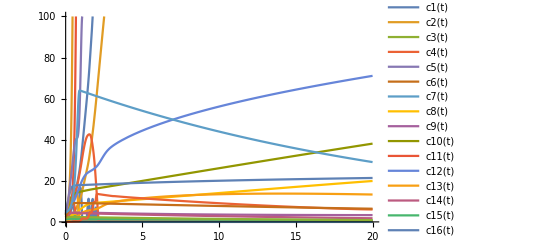

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,20},PlotLegends->vars[t],PlotRange->{0,100}]
```

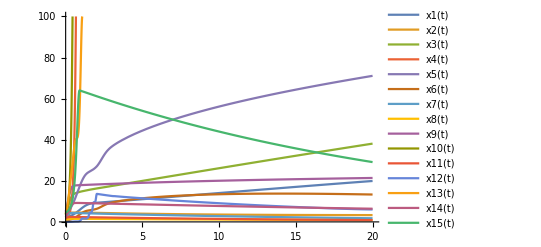

```mathematica
Plot[Evaluate[varx[t]/.try],{t,0,20},PlotLegends->varx[t],PlotRange->{0,100}]
```

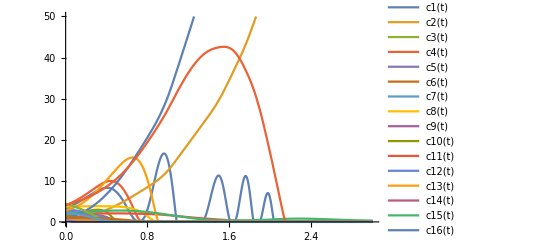

```mathematica
Plot[Evaluate[varc[t]/.prueba],{t,0,3},PlotLegends->varc[t],PlotRange->{0,50}]
```